# Oscillations in planar deficiency-one mass-action systems

Balázs Boros and Josef Hofbauer

This Mathematica Notebook is a supplementary material to the paper which has  the same title as this document. It contains some of the calculations appearing in the paper.

## 0 Focal values

Compute L_1,L_2,...,L_m, the first m focal values. Theoretical background: Chapter 4 in Dumortier, Llibre, Artés: Qualitative Theory of Planar Differential Systems.
For m=1 or 2 it runs under a second, for m=3 in less than a minute. For m=4 it takes about 20 minutes.

```mathematica
m = 4;
cd = {}; R2cd = {};
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,
    {cd=Join[cd,{Subscript[c, k,i],Subscript[d, k,i]}], R2cd = Join[R2cd,{Subscript[R, k,i]->Subscript[c, k,i]+Subscript[d, k,i] I}]}]];
coeffsxy = CoefficientList[ComplexExpand[Sum[Sum[Subscript[R, k,i] z^(k-i)(z*)^i,{i,0,k}], {k,2,2m+1}]
    /.R2cd/.{z->x+y I}], {x,y}];
cond = True;
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,
    {cond = cond && (Subscript[f, i,k-i]==ComplexExpand[Re[coeffsxy[[i+1,k-i+1]]]]) &&
    (Subscript[g, i,k-i]==ComplexExpand[Im[coeffsxy[[i+1,k-i+1]]]])}]];
cd2fg = Solve[cond,cd][[1]];

For[k=2, k≤2m+1, k++, Subscript[R, k]=Sum[Subscript[R, k,i] z^(k-i)w^i,{i,0,k}]];

(* F[i,j] computes the polynomial Subscript[F, i](Subscript[h, j]) *)
F[i_,j_] := Module[{coeffs,M,mtx},
coeffs = CoefficientList[D[Subscript[R, i] Subscript[h, j],{z,1}],{z,w}];
M = Dimensions[coeffs][[1]]-1;
mtx = (coeffs + Transpose[coeffs*]) Table[If[k+l==M&&k≠l,1/(k-l),0],{k,0,M},{l,0,M}];
I (z^Range[0,M]).mtx.w^Range[0,M]];

Subscript[h, 0] = 1;
For[k=1, k≤2m-1, k++, Subscript[h, k] = Sum[F[k+1-l,l],{l,0,k-1}]];

(* H[k,j] computes Subscript[H, k](Subscript[h, j]), note that one of k and j is even, the other is odd
    in all of the interesting cases *)
H[k_,j_] := Module[{},
coeffs = CoefficientList[Subscript[h, j],{z,w}];
Sum[Coefficient[Subscript[R, k],z^a w^(k-a)]coeffs[[((k-2a+1)+j)/2+1,(j-(k-2a+1))/2+1]],{a,(k+1-j)/2,(k+1+j)/2}]
];

For[j=1,j≤m,j++,Subscript[L, j]=Simplify[ComplexExpand[2π Re[Sum[H[2j+1-l,l],{l,0,2j-1}]]/.R2cd/.cd2fg]]];
```

The first and the second focal values are as follows. (The third and the fourth ones are very long, we don’t display them on the screen.)
Important note: f_(i,j) and g_(i,j) include the division by i!j! , so they are not simply the respective partial derivatives, but the coefficients in the Taylor series expansion.

```mathematica
Subscript[L, 1]
```

1/4 π (f_(1,2)+f_(1,1) f_(2,0)+3 f_(3,0)+f_(0,2) (f_(1,1)+2 g_(0,2))+3 g_(0,3)-g_(0,2) g_(1,1)-2 f_(2,0) g_(2,0)-g_(1,1) g_(2,0)+g_(2,1))

```mathematica
Subscript[L, 2]
```

1/48 π (3 f_(0,3) f_(1,2)-6 f_(1,1)^2 f_(1,2)+6 f_(1,4)+11 f_(0,3) f_(1,1) f_(2,0)-6 f_(1,1)^3 f_(2,0)+14 f_(1,3) f_(2,0)-37 f_(1,2) f_(2,0)^2-43 f_(1,1) f_(2,0)^3+3 f_(1,2) f_(2,1)+7 f_(1,1) f_(2,0) f_(2,1)+2 f_(1,1) f_(2,2)-9 f_(0,3) f_(3,0)-22 f_(1,1)^2 f_(3,0)-129 f_(2,0)^2 f_(3,0)+3 f_(2,1) f_(3,0)+18 f_(2,0) f_(3,1)+6 f_(3,2)-10 f_(1,1) f_(4,0)+30 f_(5,0)-41 f_(1,1) f_(1,2) g_(0,2)+16 f_(0,3) f_(2,0) g_(0,2)-43 f_(1,1)^2 f_(2,0) g_(0,2)-12 f_(2,0)^3 g_(0,2)-20 f_(2,0) f_(2,1) g_(0,2)-8 f_(2,2) g_(0,2)-109 f_(1,1) f_(3,0) g_(0,2)-44 f_(4,0) g_(0,2)-55 f_(1,2) g_(0,2)^2-53 f_(1,1) f_(2,0) g_(0,2)^2-139 f_(3,0) g_(0,2)^2+12 f_(2,0) g_(0,2)^3+5 f_(0,2)^3 (f_(1,1)+2 g_(0,2))+6 f_(0,4) (f_(1,1)+2 g_(0,2))+9 f_(0,3) g_(0,3)-24 f_(1,1)^2 g_(0,3)-139 f_(2,0)^2 g_(0,3)-3 f_(2,1) g_(0,3)-117 f_(1,1) g_(0,2) g_(0,3)-129 g_(0,2)^2 g_(0,3)+44 f_(2,0) g_(0,4)+30 g_(0,5)+4 f_(0,3) f_(1,1) g_(1,1)+4 f_(1,3) g_(1,1)-33 f_(1,2) f_(2,0) g_(1,1)-39 f_(1,1) f_(2,0)^2 g_(1,1)-117 f_(2,0) f_(3,0) g_(1,1)+5 f_(0,3) g_(0,2) g_(1,1)+8 f_(1,1)^2 g_(0,2) g_(1,1)+53 f_(2,0)^2 g_(0,2) g_(1,1)+f_(2,1) g_(0,2) g_(1,1)+39 f_(1,1) g_(0,2)^2 g_(1,1)+43 g_(0,2)^3 g_(1,1)-109 f_(2,0) g_(0,3) g_(1,1)+10 g_(0,4) g_(1,1)-8 f_(1,2) g_(1,1)^2-8 f_(1,1) f_(2,0) g_(1,1)^2-24 f_(3,0) g_(1,1)^2+43 f_(2,0) g_(0,2) g_(1,1)^2-22 g_(0,3) g_(1,1)^2+6 g_(0,2) g_(1,1)^3+3 f_(1,2) g_(1,2)+f_(1,1) f_(2,0) g_(1,2)+3 f_(3,0) g_(1,2)-20 f_(2,0) g_(0,2) g_(1,2)-3 g_(0,3) g_(1,2)+7 g_(0,2) g_(1,1) g_(1,2)-18 g_(0,2) g_(1,3)-11 f_(1,1) f_(1,2) g_(2,0)+6 f_(0,3) f_(2,0) g_(2,0)+3 f_(1,1)^2 f_(2,0) g_(2,0)+86 f_(2,0)^3 g_(2,0)-14 f_(2,0) f_(2,1) g_(2,0)-4 f_(2,2) g_(2,0)-19 f_(1,1) f_(3,0) g_(2,0)-40 f_(4,0) g_(2,0)-24 f_(1,2) g_(0,2) g_(2,0)+54 f_(1,1) f_(2,0) g_(0,2) g_(2,0)-32 f_(3,0) g_(0,2) g_(2,0)+106 f_(2,0) g_(0,2)^2 g_(2,0)-27 f_(1,1) g_(0,3) g_(2,0)-60 g_(0,2) g_(0,3) g_(2,0)+3 f_(0,3) g_(1,1) g_(2,0)+8 f_(1,1)^2 g_(1,1) g_(2,0)+133 f_(2,0)^2 g_(1,1) g_(2,0)+3 f_(2,1) g_(1,1) g_(2,0)+42 f_(1,1) g_(0,2) g_(1,1) g_(2,0)+57 g_(0,2)^2 g_(1,1) g_(2,0)+57 f_(2,0) g_(1,1)^2 g_(2,0)+6 g_(1,1)^3 g_(2,0)-10 f_(2,0) g_(1,2) g_(2,0)+5 g_(1,1) g_(1,2) g_(2,0)-6 g_(1,3) g_(2,0)-5 f_(1,2) g_(2,0)^2+11 f_(1,1) f_(2,0) g_(2,0)^2+15 f_(3,0) g_(2,0)^2+28 f_(2,0) g_(0,2) g_(2,0)^2-15 g_(0,3) g_(2,0)^2+3 f_(1,1) g_(1,1) g_(2,0)^2+9 g_(0,2) g_(1,1) g_(2,0)^2-10 f_(2,0) g_(2,0)^3-5 g_(1,1) g_(2,0)^3+f_(0,2)^2 (5 f_(1,2)-15 f_(3,0)-28 f_(2,0) g_(0,2)+15 g_(0,3)-11 g_(0,2) g_(1,1)-3 f_(1,1) (3 f_(2,0)+g_(1,1))+10 f_(2,0) g_(2,0)+5 g_(1,1) g_(2,0)-5 g_(2,1))-3 f_(0,3) g_(2,1)-8 f_(1,1)^2 g_(2,1)-55 f_(2,0)^2 g_(2,1)-3 f_(2,1) g_(2,1)-33 f_(1,1) g_(0,2) g_(2,1)-37 g_(0,2)^2 g_(2,1)-41 f_(2,0) g_(1,1) g_(2,1)-6 g_(1,1)^2 g_(2,1)-3 g_(1,2) g_(2,1)-3 f_(1,1) g_(2,0) g_(2,1)-4 g_(0,2) g_(2,0) g_(2,1)+5 g_(2,0)^2 g_(2,1)+8 f_(2,0) g_(2,2)-2 g_(1,1) g_(2,2)+6 g_(2,3)+3 f_(1,2) g_(3,0)+5 f_(1,1) f_(2,0) g_(3,0)-9 f_(3,0) g_(3,0)+16 f_(2,0) g_(0,2) g_(3,0)+9 g_(0,3) g_(3,0)+4 f_(1,1) g_(1,1) g_(3,0)+11 g_(0,2) g_(1,1) g_(3,0)+26 f_(2,0) g_(2,0) g_(3,0)+13 g_(1,1) g_(2,0) g_(3,0)-3 g_(2,1) g_(3,0)-f_(0,2) (6 f_(1,1)^3-10 f_(1,3)+4 f_(1,2) f_(2,0)+60 f_(2,0) f_(3,0)-6 f_(3,1)+106 f_(2,0)^2 g_(0,2)+10 f_(2,1) g_(0,2)+86 g_(0,2)^3-13 f_(0,3) (f_(1,1)+2 g_(0,2))+32 f_(2,0) g_(0,3)-40 g_(0,4)+3 f_(1,2) g_(1,1)+27 f_(3,0) g_(1,1)+54 f_(2,0) g_(0,2) g_(1,1)+19 g_(0,3) g_(1,1)+3 g_(0,2) g_(1,1)^2+14 g_(0,2) g_(1,2)-40 f_(2,0)^2 g_(2,0)+4 f_(2,1) g_(2,0)+40 g_(0,2)^2 g_(2,0)-42 f_(2,0) g_(1,1) g_(2,0)-11 g_(1,1)^2 g_(2,0)+4 g_(1,2) g_(2,0)+10 g_(0,2) g_(2,0)^2+f_(1,1)^2 (57 g_(0,2)+11 g_(2,0))+24 f_(2,0) g_(2,1)+11 g_(1,1) g_(2,1)-4 g_(2,2)+f_(1,1) (57 f_(2,0)^2-5 f_(2,1)+133 g_(0,2)^2+42 f_(2,0) g_(1,1)+8 g_(1,1)^2-3 g_(1,2)+42 g_(0,2) g_(2,0)+5 g_(2,0)^2-3 g_(3,0))-6 g_(0,2) g_(3,0))-4 f_(1,1) g_(3,1)-14 g_(0,2) g_(3,1)-10 g_(2,0) g_(3,1)-12 f_(2,0) g_(4,0)-6 g_(1,1) g_(4,0)+6 g_(4,1))

Good practice : compute the focal values once, and save them to a file. When needed, load from that file.

```mathematica
L1 = Subscript[L, 1]; L2 = Subscript[L, 2]; L3 = Subscript[L, 3]; L4 = Subscript[L, 4]; (* when storing in a file, better avoiding subscripts *)
DumpSave["C://path/focal_values.mx",{L1,L2,L3,L4}];
Remove["Global`*"]; (* clear all variables *)
Get["C://path/focal_values.mx"];
```

## 3 Quadrangle

### 3.1 Unstable equilibrium and a stable limit cycle

Find the positive equilibrium.

```mathematica
f = Subscript[κ, 1](Subscript[a, 2]-Subscript[a, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[a, 3]-Subscript[a, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[a, 4]-Subscript[a, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[a, 1]-Subscript[a, 4])x^Subscript[a, 4] y^Subscript[b, 4];
g = Subscript[κ, 1](Subscript[b, 2]-Subscript[b, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[b, 3]-Subscript[b, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[b, 4]-Subscript[b, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[b, 1]-Subscript[b, 4])x^Subscript[a, 4] y^Subscript[b, 4];
absubst = {Subscript[a, 1]->0, Subscript[b, 1]->1, Subscript[a, 2]->1, Subscript[b, 2]->0, Subscript[a, 3]->1, Subscript[b, 3]->2, Subscript[a, 4]->0, Subscript[b, 4]->3};
Reduce[(f/.absubst)==0 && (g/.absubst)==0 && Subscript[κ, 1]>0 && Subscript[κ, 2]>0 && Subscript[κ, 3]>0 && Subscript[κ, 4]>0 && x>0 && y>0,{x,y}]
```

κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&x==Root[#1^4 κ_2 κ_3^3-κ_1^3 κ_4&,2]&&y==κ_1/(x κ_3)

Figure out the condition for the trace being positive at the equilibrium.

```mathematica
J = D[{f,g},{{x,y}}];
xysubst = {x->((Subscript[κ, 1]^3 Subscript[κ, 4])/(Subscript[κ, 3]^3 Subscript[κ, 2]))^(1/4), y->((Subscript[κ, 1] Subscript[κ, 2])/(Subscript[κ, 3] Subscript[κ, 4]))^(1/4)};
trJ = Tr[J/.absubst]/.xysubst;
Reduce[trJ>0 && Subscript[κ, 1]>0 && Subscript[κ, 2]>0 && Subscript[κ, 3]>0 && Subscript[κ, 4]>0]
```

κ_3>0&&κ_4>0&&κ_1>0&&0<κ_2<(κ_1 κ_3 κ_4)/(κ_3^2+12 κ_3 κ_4+36 κ_4^2)

Phase portrait when the equilibrium is unstable.

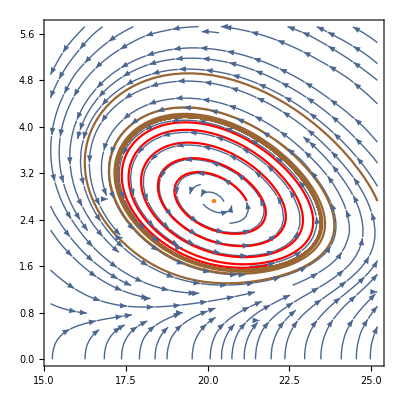

```mathematica
kappasubst = {Subscript[κ, 1]->55, Subscript[κ, 2]->1, Subscript[κ, 3]->1, Subscript[κ, 4]->1};
xytime = {x->x[t], y->y[t]};
fspec = f/.absubst/.xytime/.kappasubst;
gspec = g/.absubst/.xytime/.kappasubst;

tmax = 1.5; Subscript[x, 0] = (x/.xysubst/.kappasubst)+1; Subscript[y, 0] = (y/.xysubst/.kappasubst);
s = NDSolve[{x'[t]==fspec, y'[t]==gspec, x[0]==Subscript[x, 0], y[0]==Subscript[y, 0]}, {x,y}, {t,tmax}];
p1 = ParametricPlot[Evaluate[{x[t],y[t]}/.s], {t,0,tmax}, PlotRange->All, PlotStyle->Red];

tmax = 5; Subscript[x, 0] = (x/.xysubst/.kappasubst)+5; Subscript[y, 0] = (y/.xysubst/.kappasubst);
s = NDSolve[{x'[t]==fspec, y'[t]==gspec, x[0]==Subscript[x, 0], y[0]==Subscript[y, 0]}, {x,y}, {t,tmax}];
p2 = ParametricPlot[Evaluate[{x[t],y[t]}/.s], {t,0,tmax}, PlotRange->All, PlotStyle->Brown];

strpl = StreamPlot[{f,g}/.absubst/.kappasubst,
 {x,(x/.xysubst/.kappasubst)-5,(x/.xysubst/.kappasubst)+5}, {y,0,(y/.xysubst/.kappasubst)+3}];
pequil = ListPlot[{{x,y}/.xysubst/.kappasubst}, PlotStyle->{Orange,PointSize[Large]}];
Show[strpl,p1,p2,pequil]
```

### 3.2 Three limit cycles

Figure out where the trace vanishes.
(Note: we take the scaled ODE, thus in the paper the κ’s have overline and the positive equilibrium is at (1,1).)

```mathematica
f = Subscript[κ, 1](Subscript[a, 2]-Subscript[a, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[a, 3]-Subscript[a, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[a, 4]-Subscript[a, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[a, 1]-Subscript[a, 4])x^Subscript[a, 4] y^Subscript[b, 4];
g = K(Subscript[κ, 1](Subscript[b, 2]-Subscript[b, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[b, 3]-Subscript[b, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[b, 4]-Subscript[b, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[b, 1]-Subscript[b, 4])x^Subscript[a, 4] y^Subscript[b, 4]);
J = D[{f,g},{{x,y}}];
equilibrium = {x->1, y->1};
absubst = {Subscript[a, 1]->0, Subscript[b, 1]->1, Subscript[a, 2]->0, Subscript[b, 2]->0, Subscript[a, 3]->1, Subscript[b, 3]->2, Subscript[a, 4]->1, Subscript[b, 4]->5};
kappasubst = {Subscript[κ, 1]->γ, Subscript[κ, 2]->1, Subscript[κ, 3]->(γ+2)/3, Subscript[κ, 4]->1};
trJ = Simplify[Tr[J/.absubst/.kappasubst]/.equilibrium]
Reduce[trJ==0 && K>0 && γ>0,γ]
```

-1+K (-16+γ)

K>0&&γ==(1+16 K)/K

Store the value of γ, where the trace vanishes.

```mathematica
gammasubst = {γ->16+1/K};
```

Move the equilibrium to (0, 0), bring the equation to canonical form (i.e., the linearization at the origin is ẋ=-y, ẏ=x),
and compute the partial derivatives. These partial derivatives will then be substituted into the focal value formulas.

```mathematica
f = Subscript[κ, 1](Subscript[a, 2]-Subscript[a, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[a, 3]-Subscript[a, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[a, 4]-Subscript[a, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[a, 1]-Subscript[a, 4])x^Subscript[a, 4] y^Subscript[b, 4];
g = K(Subscript[κ, 1](Subscript[b, 2]-Subscript[b, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[b, 3]-Subscript[b, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[b, 4]-Subscript[b, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[b, 1]-Subscript[b, 4])x^Subscript[a, 4] y^Subscript[b, 4]);
J = D[{f,g},{{x,y}}]/.{x->1, y->1};
xyshift = {x->x+1, y->y+1};
f = f/.xyshift;
g = g/.xyshift;
T = {{1,0},{-aa/ω,-bb/ω}};
omegasubst = {ω->Sqrt[Det[J]]};
Tinv = Inverse[T];
Tinvuv = Tinv.{u,v};
FG = (T . {f,g})/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{aa->J[[1,1]],bb-> J[[1,2]]};
F = FG[[1]];
G = FG[[2]];
equil = {u->0,v->0};
Clear[f,g];
m = 3;
derivatives={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, derivatives = Join[derivatives, 
{Subscript[f, i,j]->(D[F,{u,i},{v,j}]/((i!)*( j!))/.equil), Subscript[g, i,j]->(D[G,{u,i},{v,j}]/((i!)*( j!))/.equil)}]]];
```

Compute the first focal value.

((-5-29 K+1250 K^2+3416 K^3) π)/(20 √2 (2+35 K)^(3/2))

K==Root0.0686Root[-5-29 #1+1250 #1^2+3416 #1^3&,3]0.06862184118263093

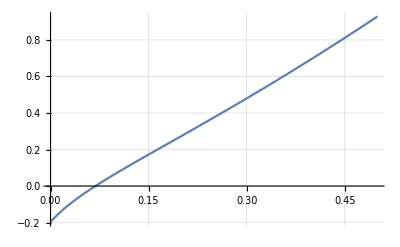

```mathematica
derivativessimplified = Simplify[derivatives/.omegasubst/.absubst/.kappasubst/.gammasubst];
Subscript[L, 1] = Simplify[L1/.derivativessimplified]
Reduce[Subscript[L, 1]==0 && K>0]
Plot[Subscript[L, 1], {K,0,1/2}, GridLines->Automatic]
```

Find out the sign of L_2 at K_0=0.0686218

```mathematica
Ksubst = {K->Root[-5-29 #1+1250 #1^2+3416 #1^3&,3]};
Subscript[L, 2] = N[L2/.derivativessimplified/.Ksubst]
```

0.0129336

Combining with permanence, this allows us to produce 3 limit cycles. However, with a little more work,
we can find parameter values for which trJ=L_1=L_2=0 and L_3<0. Thus, 3 small limit cycles can be bifurcated from the equilibrium.
We will achieve this by keeping b_4 a parameter, we will call it b.

We start by finding where the trace vanishes.
(Note:we take the scaled ODE,thus in the paper the κ's have overline and the positive equilibrium is at (1,1). We check this below.)

```mathematica
f = Subscript[κ, 1](Subscript[a, 2]-Subscript[a, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[a, 3]-Subscript[a, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[a, 4]-Subscript[a, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[a, 1]-Subscript[a, 4])x^Subscript[a, 4] y^Subscript[b, 4];
g = K(Subscript[κ, 1](Subscript[b, 2]-Subscript[b, 1])x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2](Subscript[b, 3]-Subscript[b, 2])x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3](Subscript[b, 4]-Subscript[b, 3])x^Subscript[a, 3] y^Subscript[b, 3] + Subscript[κ, 4](Subscript[b, 1]-Subscript[b, 4])x^Subscript[a, 4] y^Subscript[b, 4]);
J = D[{f,g},{{x,y}}];
equilibrium = {x->1, y->1};

absubst = {Subscript[a, 1]->0, Subscript[b, 1]->1, Subscript[a, 2]->0, Subscript[b, 2]->0, Subscript[a, 3]->1, Subscript[b, 3]->2, Subscript[a, 4]->1, Subscript[b, 4]->b};
kappasubst = {Subscript[κ, 1]->γ, Subscript[κ, 2]->1, Subscript[κ, 3]->(γ+(b-3))/(b-2), Subscript[κ, 4]->1};
f/.absubst/.kappasubst/.equilibrium
g/.absubst/.kappasubst/.equilibrium
trJ = Simplify[Tr[J/.absubst/.kappasubst]/.equilibrium]
Reduce[trJ==0 && K>0 && γ>0 && b>2,γ]
Clear[f,g];
```

0

0

-1+K (-6+3 b-b^2+γ)

b>2&&K>0&&γ==(1+6 K-3 b K+b^2 K)/K

Compute L_1, L_2, L_3 (assuming trJ=0) and plot in the (K,b)-plane where they vanish.

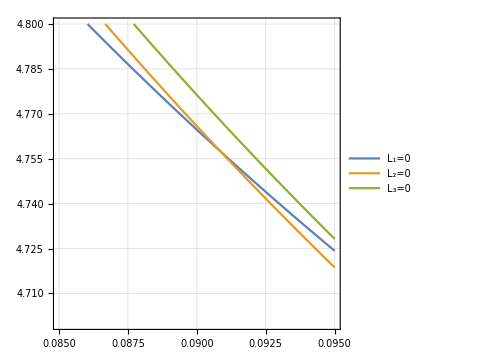
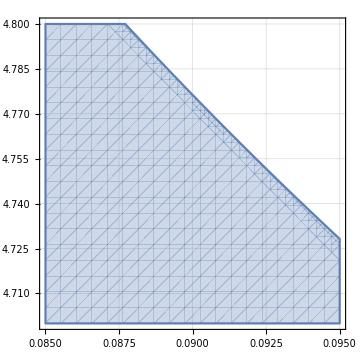

```mathematica
gammasubst = {γ->(1+6 K-3 b K+b^2 K)/K};
derivativessimplified=Simplify[derivatives/.omegasubst/.absubst/.kappasubst/.gammasubst];
Subscript[L, 1] = Simplify[L1/.derivativessimplified];
Subscript[L, 2] = Simplify[L2/.derivativessimplified];
Subscript[L, 3] = Simplify[L3/.derivativessimplified];
p1 = ContourPlot[{Subscript[L, 1]==0, Subscript[L, 2]==0, Subscript[L, 3]==0}, {K,0.085,.095}, {b,4.7,4.8}, GridLines->Automatic,
PlotLegends->{"L_1=0","L_2=0","L_3=0"}, ImageSize->Medium];
p2 = RegionPlot[Subscript[L, 3]<0, {K,0.085,.095}, {b,4.7,4.8}, GridLines->Automatic,
PlotLegends->"L_3<0", ImageSize->Medium];
Row[{p1,p2}]
```

### 3.3 Global stability of the equilibrium

We show that the divergence can be made negative for all κ exactly when a_1<a_4<a_2<a_3 and b_1<b_4<b_2<b_3 are both violated.
For symmetry reasons it suffices to check for the a_i's.

```mathematica
Subscript[A, 1] = (α-Subscript[a, 1])(Subscript[a, 1]-Subscript[a, 2]);
Subscript[A, 2] = (α-Subscript[a, 2])(Subscript[a, 2]-Subscript[a, 3]);
Subscript[A, 3] = (α-Subscript[a, 3])(Subscript[a, 3]-Subscript[a, 4]);
Subscript[A, 4] = (α-Subscript[a, 4])(Subscript[a, 4]-Subscript[a, 1]);
p1 = Reduce[Exists[α, Subscript[A, 1]≤0 && Subscript[A, 2]≤0 && Subscript[A, 3]≤0 && Subscript[A, 4]≤0 && Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4]<0]]
p2 = Reduce[Exists[α, Subscript[A, 1]≤0 && Subscript[A, 2]≤0 && Subscript[A, 3]≤0 && Subscript[A, 4]≤0 && Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4]<0] && Not[Subscript[a, 1]<Subscript[a, 4]<Subscript[a, 2]<Subscript[a, 3]]]
Reduce[Exists[α, Subscript[A, 1]≤0 && Subscript[A, 2]≤0 && Subscript[A, 3]≤0 && Subscript[A, 4]≤0 && Subscript[A, 1]+Subscript[A, 2]+Subscript[A, 3]+Subscript[A, 4]<0] && Subscript[a, 1]<Subscript[a, 4]<Subscript[a, 2]<Subscript[a, 3]]
Equal[p1,p2]
```

(a_1|a_4)∈ℝ&&((a_2<a_1&&((a_3<a_2&&(a_4≤a_2||a_4≥a_1))||a_2≤a_3≤a_1||(a_3>a_1&&a_4≤a_3)))||(a_2==a_1&&(a_3<a_1||(a_3==a_1&&(a_4<a_1||a_4>a_1))||a_3>a_1))||(a_2>a_1&&((a_3<a_1&&a_4≥a_3)||a_1≤a_3≤a_2||(a_3>a_2&&(a_4≤a_1||a_4≥a_2)))))

(a_1|a_4)∈ℝ&&((a_2<a_1&&((a_3<a_2&&(a_4≤a_2||a_4≥a_1))||a_2≤a_3≤a_1||(a_3>a_1&&a_4≤a_3)))||(a_2==a_1&&(a_3<a_1||(a_3==a_1&&(a_4<a_1||a_4>a_1))||a_3>a_1))||(a_2>a_1&&((a_3<a_1&&a_4≥a_3)||a_1≤a_3≤a_2||(a_3>a_2&&(a_4≤a_1||a_4≥a_2)))))

False

True

## 4 Chain of three reactions

Define f, g, h_1, h_2, h_3, h_4.

```mathematica
f = (Subscript[a, 2]-Subscript[a, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[a, 3]-Subscript[a, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2] + (Subscript[a, 4]-Subscript[a, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = (Subscript[b, 2]-Subscript[b, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[b, 3]-Subscript[b, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2] + (Subscript[b, 4]-Subscript[b, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3];
Psubst = {Subscript[P, 1]->{Subscript[a, 1],Subscript[b, 1]}, Subscript[P, 2]->{Subscript[a, 2],Subscript[b, 2]}, Subscript[P, 3]->{Subscript[a, 3],Subscript[b, 3]}, Subscript[P, 4]->{Subscript[a, 4],Subscript[b, 4]}};
hsubst = {Subscript[h, 1]->Det[{Subscript[P, 4]-Subscript[P, 2],Subscript[P, 3]-Subscript[P, 2]}/.Psubst],
Subscript[h, 2]->Det[{Subscript[P, 3]-Subscript[P, 1],Subscript[P, 4]-Subscript[P, 1]}/.Psubst],
Subscript[h, 3]->Det[{Subscript[P, 4]-Subscript[P, 1],Subscript[P, 2]-Subscript[P, 1]}/.Psubst],
Subscript[h, 4]->Det[{Subscript[P, 2]-Subscript[P, 1],Subscript[P, 3]-Subscript[P, 1]}/.Psubst]};
```

Verify equation (9).

```mathematica
Simplify[(Subscript[b, 3]-Subscript[b, 2])f - (Subscript[a, 3]-Subscript[a, 2])g - (-(Subscript[h, 1]+Subscript[h, 2]+Subscript[h, 3])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[h, 1] Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3]/.hsubst)]
Simplify[(Subscript[b, 4]-Subscript[b, 3])f - (Subscript[a, 4]-Subscript[a, 3])g - (+(Subscript[h, 1]+Subscript[h, 2])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] - Subscript[h, 1] Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2]/.hsubst)]
```

0

0

Verify h_1+h_2+h_3+h_4=0 and h_1+h_2=det(P_2-P_1,P_4-P_3).

```mathematica
Subscript[h, 1]+Subscript[h, 2]+Subscript[h, 3]+Subscript[h, 4]/.hsubst
Simplify[(Subscript[h, 1]+Subscript[h, 2]/.hsubst) - Det[{Subscript[P, 2]-Subscript[P, 1],Subscript[P, 4]-Subscript[P, 3]}/.Psubst]]
```

0

0

Verify the formula for the determinant of the Jacobian matrix at the equilibrium
(after the linear scaling, so the equilibrium is at (1,1), and the κ’s have overline in the paper).

```mathematica
f = (Subscript[a, 2]-Subscript[a, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[a, 3]-Subscript[a, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2] + (Subscript[a, 4]-Subscript[a, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K((Subscript[b, 2]-Subscript[b, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[b, 3]-Subscript[b, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2] + (Subscript[b, 4]-Subscript[b, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
J = D[{f,g},{{x,y}}]/.{x->1,y->1};
kappasubst={Subscript[κ, 1]->λ Subscript[h, 1], Subscript[κ, 2]->λ(Subscript[h, 1]+Subscript[h, 2]), Subscript[κ, 3]->λ(Subscript[h, 1]+Subscript[h, 2]+Subscript[h, 3])};
Simplify[(Det[J]-(Subscript[h, 1]+Subscript[h, 2]+Subscript[h, 3])/λ K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3])/.kappasubst/.hsubst]
```

0

### 4.1 Three limit cycles

Calculate f, g, h_1, h_2, h_3, and the trace.

```mathematica
absubst = {Subscript[a, 1]->0, Subscript[b, 1]->0, Subscript[a, 2]->0, Subscript[b, 2]->-q, Subscript[a, 3]->1, Subscript[b, 3]->1/2, Subscript[a, 4]->0, Subscript[b, 4]->1/2+r};
lambdasubst = {λ->-1/q};
{Subscript[h, 1],Subscript[h, 2],Subscript[h, 3]}/.hsubst/.absubst
{f,g}/.kappasubst/.hsubst/.absubst/.lambdasubst
trJ = Simplify[Tr[J/.kappasubst/.hsubst/.absubst/.lambdasubst]]
Reduce[trJ==0 && K>0 && q>0 && r>0, K]
```

{-1/2-q-r,1/2+r,0}

{-x √y+y^-q,K (-1/2-q-r+r x √y+(1/2+q) y^-q)}

-1-K q (1/2+q)+(K r)/2

q>0&&r>q+2 q^2&&K==2/(-q-2 q^2+r)

Move the equilibrium to (0, 0), bring the equation to canonical form (i.e., the linearization at the origin is ẋ=-y, ẏ=x),
and compute the partial derivatives. These partial derivatives will then be substituted into the focal value formulas.

```mathematica
f = (Subscript[a, 2]-Subscript[a, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[a, 3]-Subscript[a, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2] + (Subscript[a, 4]-Subscript[a, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K((Subscript[b, 2]-Subscript[b, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[b, 3]-Subscript[b, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2] + (Subscript[b, 4]-Subscript[b, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
J = D[{f,g},{{x,y}}]/.{x->1, y->1};
xyshift = {x->x+1, y->y+1};
f = f/.xyshift;
g = g/.xyshift;
T = {{1,0},{-aa/ω,-bb/ω}};
omegasubst = {ω->Sqrt[Det[J]]};
Tinv = Inverse[T];
Tinvuv = Tinv.{u,v};
FG = (T . {f,g})/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{aa->J[[1,1]],bb-> J[[1,2]]};
F = FG[[1]];
G = FG[[2]];
equil = {u->0,v->0};
Clear[f,g];
m = 3;
derivatives = {};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, derivatives = Join[derivatives,
{Subscript[f, i,j]->(D[F,{u,i},{v,j}]/((i!)*( j!))/.equil), Subscript[g, i,j]->(D[G,{u,i},{v,j}]/((i!)*( j!))/.equil)}]]];
```

Compute the first focal value and check where it vanishes.

```mathematica
Ksubst = {K->2/(r-q(1+2 q))};
derivativessimplified = 
Simplify[derivatives/.omegasubst/.kappasubst/.hsubst/.absubst/.lambdasubst/.Ksubst];
Subscript[L, 1] = Simplify[L1/.derivativessimplified]
Reduce[Subscript[L, 1]==0 && q>0 && r>q(2q+1)]
```

-(π r (16 q^2+4 q^3-3 r+q (7+6 r)))/(8 (1+2 q) (q+2 q^2-r)^2 √(-(q (1+2 q+2 r))/(q+2 q^2-r)))

0<q<1/2&&r==(-7 q-16 q^2-4 q^3)/(-3+6 q)

Compute the second focal value and check where it vanishes.

-(π √(3+2 q) (7+2 q)^2 (3-14 q+8 q^2))/(1536 (1+2 q)^4)

q==1/4

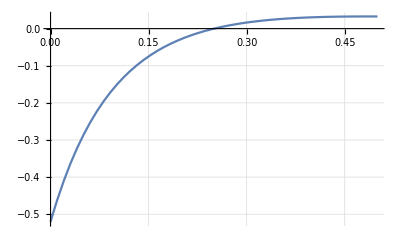

```mathematica
rsubst = {r->(-7 q-16 q^2-4 q^3)/(-3+6 q)};
Subscript[L, 2] = Simplify[L2/.derivativessimplified/.rsubst]
Reduce[Subscript[L, 2]==0 && 0<q<1/2]
Plot[Subscript[L, 2], {q,0,1/2}, GridLines->Automatic]
```

Back substitute to get r and K. Check the sign of L_3.

```mathematica
qsubst = {q->1/4}
rsubst/.qsubst
Ksubst/.rsubst/.qsubst
Subscript[L, 3] = Simplify[L3/.derivativessimplified/.rsubst/.qsubst]
```

{q→1/4}

{r→15/8}

{K→4/3}

-(625 √(7/2) π)/110592

### 4.2 Reversible center

Check κ_1, κ_2, κ_3 (with overline), the r.h.s. of the ODE, and the Jacobian at the equilibrium (1,1).

```mathematica
f = (Subscript[a, 2]-Subscript[a, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1]+(Subscript[a, 3]-Subscript[a, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2]+(Subscript[a, 4]-Subscript[a, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K((Subscript[b, 2]-Subscript[b, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1]+(Subscript[b, 3]-Subscript[b, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2]+(Subscript[b, 4]-Subscript[b, 3])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
absubst = {Subscript[a, 1]->0, Subscript[b, 1]->0, Subscript[a, 2]->p, Subscript[b, 2]->q, Subscript[a, 3]->q, Subscript[b, 3]->p, Subscript[a, 4]->q-p, Subscript[b, 4]->p+q^2/p};
Ksubst = {K->-p/q};
lambdasubst = {λ->-1/(p^2-q^2)};
Simplify[{Subscript[κ, 1],Subscript[κ, 2],Subscript[κ, 3]}/.kappasubst/.hsubst/.absubst/.Ksubst/.lambdasubst]
fg = {f,g}/.kappasubst/.hsubst/.absubst/.Ksubst/.lambdasubst;
Simplify[fg]
MatrixForm[Simplify[J/.kappasubst/.hsubst/.absubst/.Ksubst/.lambdasubst]]
```

{1-q/p,-q/(p-q),1}

{p-p x^q y^p+q (-1+x^p y^q),q-q x^q y^p+p (-1+x^p y^q)}

(0 | -p^2+q^2
p^2-q^2 | 0)

Plot the toric rays that are asymptotic to the homoclinic orbit.

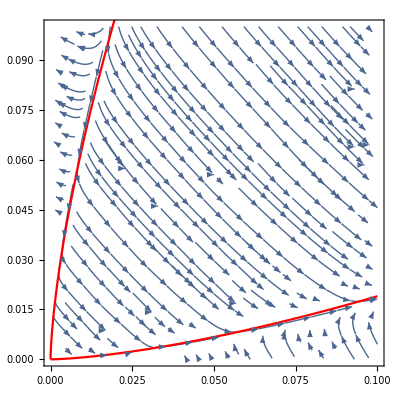

```mathematica
pqsubst = {p->3/2, q->-1};
strpl = StreamPlot[fg/.pqsubst, {x,0,1/10}, {y,0,1/10}];
toric1 = Plot[x^(-p/q)((p-q)/p)^(1/q)/.pqsubst, {x,0,1/10}, PlotStyle->Red];
toric2 = Plot[x^(-q/p)((p-q)/p)^(1/p)/.pqsubst, {x,0,1/10}, PlotStyle->Red];
Show[strpl,toric1,toric2]
```

## 5 Three reactions

Verify equation (18).

```mathematica
f = Subscript[κ, 1] Subscript[c, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[c, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[c, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = Subscript[κ, 1] Subscript[d, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[d, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[d, 3] x^Subscript[a, 3] y^Subscript[b, 3];
Simplify[Subscript[d, 2] f - Subscript[c, 2] g - (+(Subscript[c, 1] Subscript[d, 2]-Subscript[c, 2] Subscript[d, 1])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] - (Subscript[c, 2] Subscript[d, 3]-Subscript[c, 3] Subscript[d, 2])Subscript[κ, 3] x^Subscript[a, 3] y^Subscript[b, 3]/.hsubst)]
Simplify[Subscript[d, 3] f - Subscript[c, 3] g - (-(Subscript[c, 3] Subscript[d, 1]-Subscript[c, 1] Subscript[d, 3])Subscript[κ, 1] x^Subscript[a, 1] y^Subscript[b, 1] + (Subscript[c, 2] Subscript[d, 3]-Subscript[c, 3] Subscript[d, 2])Subscript[κ, 2] x^Subscript[a, 2] y^Subscript[b, 2]/.hsubst)]
```

0

0

Verify equation (23) on the determinant of the Jacobian matrix.

```mathematica
f = Subscript[κ, 1] Subscript[c, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[c, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[c, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K(Subscript[κ, 1] Subscript[d, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[d, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[d, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
kappasubst = {Subscript[κ, 1]->λ(Subscript[c, 2] Subscript[d, 3]-Subscript[c, 3] Subscript[d, 2]), Subscript[κ, 2]->λ(Subscript[c, 3] Subscript[d, 1]-Subscript[c, 1] Subscript[d, 3]), Subscript[κ, 3]->λ(Subscript[c, 1] Subscript[d, 2]-Subscript[c, 2] Subscript[d, 1])};
xstar = 1;
ystar = 1;
J = D[{f,g},{{x,y}}]/.{x->1,y->1};
Simplify[(Det[J]-1/λ K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3](Subscript[a, 1](Subscript[b, 2]-Subscript[b, 3])+Subscript[a, 2](Subscript[b, 3]-Subscript[b, 1])+Subscript[a, 3](Subscript[b, 1]-Subscript[b, 2])))/.kappasubst]
```

0

### 5.1 Four limit cycles

Check where the trace vanishes.

```mathematica
f = Subscript[κ, 1] Subscript[c, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[c, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[c, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K(Subscript[κ, 1] Subscript[d, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[d, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[d, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
abcdsubst = {Subscript[a, 1]->0, Subscript[b, 1]->0, Subscript[c, 1]->0, Subscript[d, 1]->-1, Subscript[a, 2]->0, Subscript[b, 2]->-1, Subscript[c, 2]->1, Subscript[d, 2]->-1, Subscript[a, 3]->a, Subscript[b, 3]->b, Subscript[c, 3]->-1, Subscript[d, 3]->d};
kappasubst = {Subscript[κ, 1]->λ(Subscript[c, 2] Subscript[d, 3]-Subscript[c, 3] Subscript[d, 2]), Subscript[κ, 2]->λ(Subscript[c, 3] Subscript[d, 1]-Subscript[c, 1] Subscript[d, 3]), Subscript[κ, 3]->λ(Subscript[c, 1] Subscript[d, 2]-Subscript[c, 2] Subscript[d, 1])};
lambdasubst = {λ->1};
fg = {f,g}/.kappasubst/.abcdsubst/.lambdasubst
J = D[fg,{{x,y}}]/.{x->1,y->1};
Reduce[Tr[J]==0 && a>0 && b>-1 && d>0 && 1+b d>0,K]
```

{1/y-x^a y^b,K (1-d-1/y+d x^a y^b)}

((0<d≤1&&b>-1&&a>0)||(d>1&&b>-1/d&&a>0))&&K==a/(1+b d)

Store the value for K that makes the trace zero.

```mathematica
Ksubst = {K->a/(1+b d)};
```

Move the equilibrium to (0, 0), bring the equation to canonical form (i.e., the linearization at the origin is ẋ=-y, ẏ=x),
and compute the partial derivatives (up to order 9). These partial derivatives will then be substituted into the focal value formulas.

```mathematica
f = Subscript[κ, 1] Subscript[c, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[c, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[c, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K(Subscript[κ, 1] Subscript[d, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[d, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[d, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
J = D[{f,g},{{x,y}}]/.{x->1, y->1};
xyshift = {x->x+1, y->y+1};
f = f/.xyshift;
g = g/.xyshift;
T = {{1,0},{-aa/ω,-bb/ω}};
omegasubst = {ω->Sqrt[Det[J]]};
Tinv = Inverse[T];
Tinvuv = Tinv.{u,v};
FG = (T . {f,g})/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{aa->J[[1,1]],bb-> J[[1,2]]};
F = FG[[1]];
G = FG[[2]];
equil = {u->0,v->0};
Clear[f,g];
m = 4;
derivatives = {};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, derivatives = Join[derivatives, 
{Subscript[f, i,j]->(D[F,{u,i},{v,j}]/((i!)*( j!))/.equil), Subscript[g, i,j]->(D[G,{u,i},{v,j}]/((i!)*( j!))/.equil)}]]];
```

Compute the first focal value and check where it vanishes.

```mathematica
derivativessimplified = 
Simplify[derivatives/.omegasubst/.Ksubst/.kappasubst/.abcdsubst/.lambdasubst];
Subscript[L, 1] = Simplify[L1/.derivativessimplified]
Reduce[Subscript[L, 1]==0 && a>0 && d>1 && 1+b d>0,b]
```

(a (a+2 a^2 d+a b d-(1+b d)^2) π)/(8 √((a^2 (-1+d))/(1+b d)) (1+b d)^2)

a>0&&d>1&&b==(-2+a)/(2 d)+1/2 √((a^2+8 a^2 d)/d^2)

Let' s see the second, third, and fourth focal values. They get complicated. (The computation of L_4 may take a few minutes.)

```mathematica
bsubst = {b->(-2+a(1+√(1+8  d)))/(2 d)};
Subscript[L, 2] = Simplify[FullSimplify[L2/.derivativessimplified]/.bsubst]
Subscript[L, 3] = Simplify[FullSimplify[L3/.derivativessimplified]/.bsubst]
Subscript[L, 4] = Simplify[FullSimplify[L4/.derivativessimplified]/.bsubst]
```

(a (-(-1+d) (68 d^2+2 d (-5+√(1+8 d))-3 (1+√(1+8 d)))+a^2 (-1+d) (3 (1+√(1+8 d))+2 d^2 (11+√(1+8 d))+d (23+11 √(1+8 d)))+a (12 d^3 √(1+8 d)+6 (1+√(1+8 d))+3 d (9+√(1+8 d))-d^2 (57+29 √(1+8 d)))) π)/(18 √2 √((a (-1+d))/(1+√(1+8 d))) (1+√(1+8 d))^4 (-2+a+2 d+a √(1+8 d)))

-((a^2 ((-1+d)^3 (972 d^3+d (893-55 √(1+8 d))+237 (1+√(1+8 d))-2 d^2 (2431+491 √(1+8 d)))+2 a^2 (-1+d) (264 d^6+702 (1+√(1+8 d))-40 d^2 (-149+52 √(1+8 d))+2 d^5 (613+483 √(1+8 d))+6 d (1037+569 √(1+8 d))-3 d^3 (8351+3687 √(1+8 d))-d^4 (24805+3769 √(1+8 d)))-a (-1+d)^2 (-942 (1+√(1+8 d))+d^4 (9758+450 √(1+8 d))-2 d (2975+1091 √(1+8 d))+d^3 (21647+4931 √(1+8 d))+d^2 (5813+7397 √(1+8 d)))+a^4 (-1+d) (231 (1+√(1+8 d))+4 d^5 (703+31 √(1+8 d))+11 d (335+251 √(1+8 d))+14 d^4 (1599+257 √(1+8 d))+d^2 (19083+9887 √(1+8 d))+d^3 (36475+11623 √(1+8 d)))+a^3 (120 d^7+930 (1+√(1+8 d))+28 d^6 (493+44 √(1+8 d))+10 d (1061+689 √(1+8 d))+d^2 (25893+5773 √(1+8 d))+d^5 (533+6985 √(1+8 d))-d^4 (71103+15067 √(1+8 d))-d^3 (23123+20855 √(1+8 d)))) π)/(72 √2 ((a (-1+d))/(1+√(1+8 d)))^(3/2) (1+√(1+8 d))^7 (-2+a+2 d+a √(1+8 d))^2))

(√((a (-1+d))/(1+√(1+8 d))) (3 (-1+d)^5 (-1350168 d^4+1825044 (1+√(1+8 d))+8 d (1039715+127193 √(1+8 d))+4 d^3 (-1942467+275354 √(1+8 d))-d^2 (32194101+13237315 √(1+8 d)))+2 a (-1+d)^4 (16314192 (1+√(1+8 d))+20 d^5 (746612+52299 √(1+8 d))+6 d (20372149+9496021 √(1+8 d))-d^4 (363681203+36949049 √(1+8 d))-2 d^3 (321024423+99959585 √(1+8 d))-d^2 (33552995+133752833 √(1+8 d)))+12 a^6 (-1+d) (437415 (1+√(1+8 d))+8 d^8 (799993+23231 √(1+8 d))+16 d^7 (8299934+811265 √(1+8 d))+d (10587487+8837827 √(1+8 d))+19 d^5 (64786897+18235757 √(1+8 d))+6 d^3 (75001813+39832137 √(1+8 d))+2 d^6 (328894755+59699281 √(1+8 d))+d^2 (98782836+66930848 √(1+8 d))+d^4 (1052537463+419188895 √(1+8 d)))-4 a^2 (-1+d)^3 (2333160 d^7-20252799 (1+√(1+8 d))+d^6 (132972559+11159685 √(1+8 d))-d^2 (377742403+18933343 √(1+8 d))-3 d (70406353+43402621 √(1+8 d))+2 d^5 (416513618+59027017 √(1+8 d))+5 d^4 (390575233+108024339 √(1+8 d))+d^3 (894225897+567337183 √(1+8 d)))+4 a^5 (1129632 d^10+d^4 (267696186-904979838 √(1+8 d))+7930944 (1+√(1+8 d))+8 d^9 (22872659+1162683 √(1+8 d))+18 d^7 (38132353+33877975 √(1+8 d))+3 d (50904457+40329865 √(1+8 d))+4 d^8 (351507807+57831427 √(1+8 d))-13 d^5 (471734401+192198281 √(1+8 d))+4 d^3 (611285790+203687477 √(1+8 d))+d^2 (1006640779+586129951 √(1+8 d))-d^6 (5484544993+796821389 √(1+8 d)))+4 a^3 (-1+d)^2 (d^3 (56591601-679837695 √(1+8 d))+26815896 (1+√(1+8 d))+72 d^8 (220198+5515 √(1+8 d))+120 d^2 (10519564+3933431 √(1+8 d))+4 d^7 (10082069+6086434 √(1+8 d))+6 d (59746561+41869297 √(1+8 d))-d^6 (1454017215+132100123 √(1+8 d))-d^5 (5198444217+1151299573 √(1+8 d))-d^4 (4753010123+2026566983 √(1+8 d)))+4 a^4 (-1+d) (19970109 (1+√(1+8 d))+12 d^9 (825499+7431 √(1+8 d))-27 d^6 (175810871+19459271 √(1+8 d))+12 d (27142822+20486119 √(1+8 d))+d^8 (378439718+34608994 √(1+8 d))+d^7 (378911879+246975083 √(1+8 d))+d^3 (2278163397+257610265 √(1+8 d))-4 d^5 (2323240174+705361543 √(1+8 d))+d^2 (1660617107+837044267 √(1+8 d))-d^4 (3428684549+2434223729 √(1+8 d)))) π)/(64800 √2 (-1+d)^3 (1+√(1+8 d))^7 (-2+a+2 d+a √(1+8 d))^3)

Plot the curve in the (a,d) plane where L_2 vanishes.

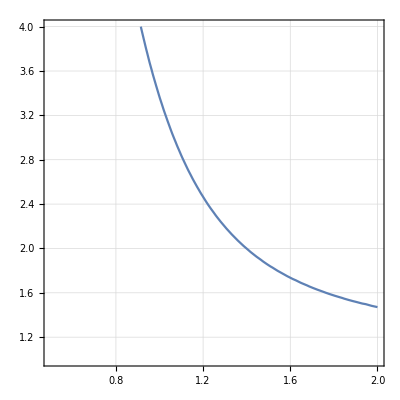

```mathematica
ContourPlot[Subscript[L, 2]==0, {a,1/2,2}, {d,1,4}, GridLines->Automatic]
```

Take the enumerator of L_2, it is quadratic in "a", so we can solve L_2=0 explicitly. We choose that root, which gives positive value for "a".

```mathematica
L2enumerator = (-(-1+d) (68 d^2+2 d (-5+√(1+8 d))-3 (1+√(1+8 d)))+
a^2 (-1+d) (3 (1+√(1+8 d))+2 d^2 (11+√(1+8 d))+d (23+11 √(1+8 d)))+
a (12 d^3 √(1+8 d)+6 (1+√(1+8 d))+3 d (9+√(1+8 d))-d^2 (57+29 √(1+8 d))));
c = CoefficientList[L2enumerator,a];
asubst = Simplify[{a->(-c[[2]]+Sqrt[c[[2]]^2-4 c[[3]]c[[1]]])/(2 c[[3]])}]
Clear[c]
Reduce[(a/.asubst)>0 && d>1]
```

{a→(-6-6 √(1+8 d)-12 d^3 √(1+8 d)-3 d (9+√(1+8 d))+d^2 (57+29 √(1+8 d))+√2 √(d^2 (576 d^5+169 (1+√(1+8 d))+8 d^4 (43+34 √(1+8 d))+2 d (407+69 √(1+8 d))+4 d^3 (36+79 √(1+8 d))-d^2 (1471+703 √(1+8 d)))))/(2 (-1+d) (3 (1+√(1+8 d))+2 d^2 (11+√(1+8 d))+d (23+11 √(1+8 d))))}

d>1

Plug in the above "a" to L_3 and L_4 and let's see numerically what the sign of L_4 is, where L_3 vanishes.

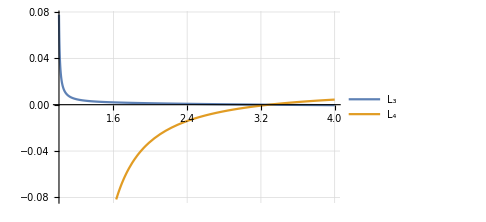
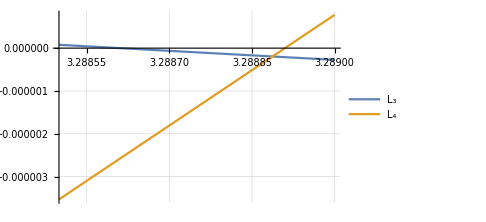

```mathematica
L3d = Simplify[Subscript[L, 3]/.asubst];
L4d = Simplify[Subscript[L, 4]/.asubst];
p1 = Plot[{L3d,L4d}, {d,1.01,4}, PlotLegends->{"L_3","L_4"}, GridLines->Automatic,
ImageSize->Medium];
p2 = Plot[{L3d,L4d}, {d,3.2885,3.2890}, PlotLegends->{"L_3","L_4"}, GridLines->Automatic,
ImageSize->Medium];
Row[{p1,p2}]
```

Thus, we numerically found that there exist parameter values such that trJ=L_1=L_2=L_3=0 and L_4<0.

### 5.2 Reversible center

Verify the trace and the determinant formula in the proof of Proposition 6.

```mathematica
f = Subscript[κ, 1] Subscript[c, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[c, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[c, 3] x^Subscript[a, 3] y^Subscript[b, 3];
g = K(Subscript[κ, 1] Subscript[d, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[d, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[d, 3] x^Subscript[a, 3] y^Subscript[b, 3]);
absubst = {Subscript[a, 1]->0, Subscript[b, 1]->0, Subscript[a, 2]->p, Subscript[b, 2]->q, Subscript[a, 3]->q, Subscript[b, 3]->p};
kappasubst = {Subscript[κ, 1]->λ(Subscript[c, 2] Subscript[d, 3]-Subscript[c, 3] Subscript[d, 2]), Subscript[κ, 2]->λ(Subscript[c, 3] Subscript[d, 1]-Subscript[c, 1] Subscript[d, 3]), Subscript[κ, 3]->λ(Subscript[c, 1] Subscript[d, 2]-Subscript[c, 2] Subscript[d, 1])};
J=D[{f,g},{{x,y}}]/.{x->1,y->1};
Simplify[(Det[J]-1/λ K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3](p^2-q^2))/.kappasubst/.absubst]
Simplify[(Tr[J]-(p(Subscript[c, 2] Subscript[κ, 2]+K Subscript[d, 3] Subscript[κ, 3])+q(Subscript[c, 3] Subscript[κ, 3]+K Subscript[d, 2] Subscript[κ, 2])))/.kappasubst/.absubst]
```

0

0

### 5.3 Liénard center

Verify the trace and the determinant formula in the proof of Proposition 7.

```mathematica
absubst = {Subscript[a, 1]->1, Subscript[b, 1]->0, Subscript[a, 2]->0, Subscript[b, 2]->-1/2, Subscript[a, 3]->0, Subscript[b, 3]->-2};
xdot = (Subscript[κ, 1] Subscript[c, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[c, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[c, 3] x^Subscript[a, 3] y^Subscript[b, 3])/.absubst;
ydot = (K(Subscript[κ, 1] Subscript[d, 1] x^Subscript[a, 1] y^Subscript[b, 1] + Subscript[κ, 2] Subscript[d, 2] x^Subscript[a, 2] y^Subscript[b, 2] + Subscript[κ, 3] Subscript[d, 3] x^Subscript[a, 3] y^Subscript[b, 3]))/.absubst;
kappasubst = {Subscript[κ, 1]->λ(Subscript[c, 2] Subscript[d, 3]-Subscript[c, 3] Subscript[d, 2]), Subscript[κ, 2]->λ(Subscript[c, 3] Subscript[d, 1]-Subscript[c, 1] Subscript[d, 3]), Subscript[κ, 3]->λ(Subscript[c, 1] Subscript[d, 2]-Subscript[c, 2] Subscript[d, 1])};
J=D[{xdot,ydot},{{x,y}}]/.{x->1,y->1};
Simplify[(Det[J]-3/2 1/λ K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3])/.kappasubst/.absubst]
Simplify[(Tr[J]-(Subscript[c, 1] Subscript[κ, 1]-1/2 K Subscript[d, 2] Subscript[κ, 2]-2K Subscript[d, 3] Subscript[κ, 3]))/.kappasubst/.absubst]
```

0

0

Check ÿ+f(y)ẏ+g(y)=0 in the proof of Proposition 7.

```mathematica
xyshift = {x->x[τ]+1, y->y[τ]+1};
xdot = xdot/.xyshift;
ydot = ydot/.xyshift;
f = -Subscript[c, 1] Subscript[κ, 1] + 1/2 K Subscript[d, 2] Subscript[κ, 2](y[τ]+1)^(-3/2) + 2K Subscript[d, 3] Subscript[κ, 3](y[τ]+1)^-3;
g = 1/λ K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3]((y[τ]+1)^(-1/2) - (y[τ]+1)^-2);
yddot=D[ydot,τ];
FullSimplify[(yddot+f ydot+g)/.{x'[τ]->xdot, y'[τ]->ydot}/.{Subscript[κ, 2]->λ(Subscript[c, 3] Subscript[d, 1]-Subscript[c, 1] Subscript[d, 3]), Subscript[κ, 3]->λ(Subscript[c, 1] Subscript[d, 2]-Subscript[c, 2] Subscript[d, 1])}]
```

0

Compute the integrals F(x)=(∫_0)^x f(y)dy and G(x)=(∫_0)^x g(y)dy in the proof of Proposition 7. Then verify F=α G^2+β G.

```mathematica
F = Assuming[x>0, Integrate[f/.{y[τ]->y}, {y,0,x}]]
G = Assuming[x>0, Integrate[g/.{y[τ]->y}, {y,0,x}]]
Simplify[α G^2+β G-F/.{α->-λ^2/4(Subscript[c, 1] Subscript[κ, 1])/(K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3])^2, β->-(3λ)/2(Subscript[c, 1] Subscript[κ, 1])/(K Subscript[κ, 1] Subscript[κ, 2] Subscript[κ, 3])}/.{Subscript[κ, 2]->(Subscript[c, 1] Subscript[κ, 1])/(K Subscript[d, 2]), Subscript[κ, 3]->(Subscript[c, 1] Subscript[κ, 1])/(4K Subscript[d, 3])}]
```

-x c_1 κ_1+1/2 K (2-2/(√(1+x))) d_2 κ_2+(K x (2+x) d_3 κ_3)/(1+x)^2

(K (-2-3 x+2 √(1+x)+2 x √(1+x)) κ_1 κ_2 κ_3)/((1+x) λ)

0

## 6 Zigzag

Find the positive equilibrium.

```mathematica
f = y^3-3x y^2+(1+κ)y;
g = -y^3+x y^2+(1-κ)y;
Reduce[f==0 && g==0 && x>0 && y>0 && κ>0, {y,x}]
```

0<κ<2&&y==√(2-κ)&&x==-(-y-y^3-y κ)/(3 y^2)

```mathematica
Simplify[-(-y-y^3-y κ)/(3 y^2)/.{y->√(2-κ)}]
```

1/(√(2-κ))

Compute the trace at the equilibrium.

```mathematica
equilibrium={x->1/(√(2-κ)), y->√(2-κ)};
J = D[{f,g},{{x,y}}]/.equilibrium;
Simplify[Tr[J]]
```

-9+5 κ

Compute the first focal value for κ=9/5.

```mathematica
f = y^3-3x y^2+(1+κ)y;
g = -y^3+x y^2+(1-κ)y;
omegasubst = {ω->Sqrt[Det[J]]};
shift = {x->x+(x/.equilibrium), y->y+(y/.equilibrium)};
f = f/.shift;
g = g/.shift;
T = {{1,0},{-aa/ω,-bb/ω}};
Tinv = Inverse[T];
Tinvuv = Tinv.{u,v};
FG = (T . {f,g})/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{aa->J[[1,1]],bb-> J[[1,2]]};
F = FG[[1]];
G = FG[[2]];
equil = {u->0,v->0};
Clear[f,g];
m = 1;
derivatives = {};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, derivatives = Join[derivatives,
{Subscript[f, i,j]->(D[F,{u,i},{v,j}]/((i!)*( j!))/.{u->0,v->0}), Subscript[g, i,j]->(D[G,{u,i},{v,j}]/((i!)*( j!))/.{u->0,v->0})}]]];
Simplify[L1/.derivatives/.omegasubst/.{κ->9/5}]
```

(5 π)/13

Since L_1>0, the Andronov-Hopf bifurcation is subcritical.
We demonstrate the existence of an unstable limit cycle for κ slightly smaller than 9/5.

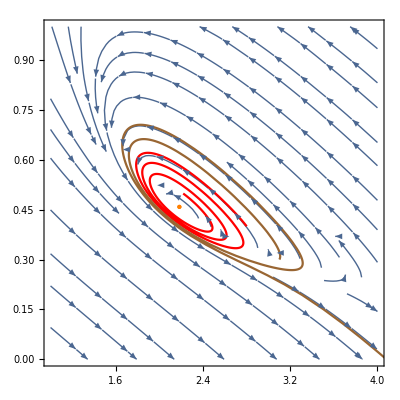

```mathematica
f = y^3-3x y^2+(1+κ)y;
g = -y^3+x y^2+(1-κ)y;
xytime = {x->x[t], y->y[t]};
kappaspec = {κ->1.79};

tmax = 50; Subscript[x, 0] = 2.8; Subscript[y, 0] = 0.4;
s = NDSolve[{x'[t]==(f/.xytime/.kappaspec), y'[t]==(g/.xytime/.kappaspec), x[0]==Subscript[x, 0], y[0]==Subscript[y, 0]},
{x,y}, {t,tmax}];
p1 = ParametricPlot[Evaluate[{x[t],y[t]}/.s], {t,0,tmax}, PlotRange->All, PlotStyle->Red];

tmax = 50; Subscript[x, 0] = 3.1; Subscript[y, 0] = 0.3;
s = NDSolve[{x'[t]==(f/.xytime/.kappaspec), y'[t]==(g/.xytime/.kappaspec), x[0]==Subscript[x, 0], y[0]==Subscript[y, 0]},
{x,y}, {t,tmax}];
p2 = ParametricPlot[Evaluate[{x[t],y[t]}/.s], {t,0,tmax}, PlotRange->All, PlotStyle->Brown];

pequil = ListPlot[{{1/Sqrt[2-κ],Sqrt[2-κ]}/.kappaspec}, PlotStyle->{Orange, PointSize[Large]}];
strpl = StreamPlot[{f,g}/.kappaspec, {x,1,4}, {y,0,1}, LabelStyle->"Subtitle"];
Show[strpl,p1,p2,pequil]
```